```mathematica
NN = 3
```

3

```mathematica
maxr = 100
maxk = 100
CMSz[a_] := Exp[1/NN Log[a]]/Exp[1/NN Log[-(1 - a)]]∑_(r=1)^maxr NN/(r NN + 1)( 1 - 1/(1 - a))^r
CMSzsimple[a_] := Exp[1/NN Log[a]]/Exp[1/NN ⅈ π] a
CMSzsimple1[a_] := Exp[1/NN Log[a]]/Exp[1/NN Log[-(1 - a)]] a
```

100

100

```mathematica
m0[a_] := ⅇ^(1/NN Log[a])

σ0[a_] := ⅇ^(1/NN Log[ 1 + a])



mj[a_,j_] := m0[a] ⅇ^(2 π ⅈ j / NN)

m1[a_] := m0[a] ⅇ^(2 π ⅈ  / NN)

σ1[a_] := σ0[a]  ⅇ^((2 π ⅈ)/NN)



W0[a_] := - NN σ0[a] - ∑_(j=0)^(NN-1) mj[a,j] Log[ σ0[a] - mj[a,j] ]



W1[a_] := - NN σ1[a] - ∑_(j=0)^(NN-1) mj[a,j] Log[ σ1[a] - mj[a,j] ]



CMS[a_] := (- NN σ0[a] ( ⅇ^((2 π ⅈ)/NN) - 1) - ∑_(j=0)^(NN-1) mj[a,j] ( Log[ σ1[a] - mj[a,j] ] - Log [ σ0[a] - mj[a,j] ] ))/(m1[a] - m0[a])

CMSFrac[a_, q1_, q2_] := CMS[a]  +  2 π ⅈ q1  +  (2 π ⅈ q2 ( mj[a,2] - m0[a] ))/(m1[a] - m0[a])



CMSleft[a_] := CMSFrac[a, -1/3, -1/3]




CMSright[a_] := CMSFrac[a, +1/3, +1/3]


CMSFrac2[a_,s_,q1_] := (W1[a] - W0[a]  +  2 π ⅈ ( s + q1 ) ( m1[a] - m0[a] ))/(mj[a,2] - m0[a])


CMSE[a_] :=  (- NN σ0[a] ( ⅇ^((2 π ⅈ)/NN) - 1) - ∑_(j=0)^(NN-1) mj[a,j] ( Log[ 1 - mj[a,j]/σ1[a] ] - Log [ 1 - mj[a,j]/σ0[a] ] ))/(m1[a] - m0[a])
CMSm[a_] := - NN σ0[a]/m0[a]( 1 - ∑_(k=1)^maxk (a/(1 + a))^k/(k NN - 1) )
CMSmN[a_] := - NN σ0[a]/m0[a]( 1 + 1/NN Log [ 1/(1 + a)] )
```

```mathematica
MM= 400;
XY  = Table[{Null, Null}, {MM}];
XY1  = Table[{Null, Null}, {MM}];
XYgen  = Table[{Null, Null}, {MM}];
XYE  = Table[{Null, Null}, {MM}];
XYm = Table[{Null, Null}, {MM}];
XYmN = Table[{Null, Null}, {MM}];
centre = 0;
width = 360;
For [ j = 0, j < MM, j++, 
ϕ = π/180(centre - width/2+ (width j)/MM);
(*
a0 = 1.0 ⅇ^(ⅈ ϕ);
 z = a /. FindRoot[ { Re[CMSzsimple[a]] == 0 }, {a, a0}];
XY[[j+1]] = { -1 +Re[z], Im[z] };
a01 = 0.5 ⅇ^(ⅈ ϕ);
z1 = a /. FindRoot[ { Re[CMSz[a]] == 0 }, {a, a01}];
XY1[[j+1]] = { -1 +Re[z1], Im[z1] };
*)

x = -1.2 + ( 10 + 1.2)/MM j;
a0gen = 3.0 ⅇ^(ⅈ ϕ);
(* a0gen = -1/2 + ⅈ (2.0 + (10.-2.)/MM j ); *)
zgen = a /. FindRoot[ { Re[CMS[a]] == 0 }, {a, a0gen}];
XYgen[[j+1]] = { Re[zgen], Im[zgen] };

(*
a0E =  3.0 ⅇ^(ⅈ ϕ);
zE = a /. FindRoot[ { Re[CMSE[a]] == 0 }, {a, a0E}];
XYE[[j+1]] = { Re[zE], Im[zE] };

a0m = 3.0 ⅇ^(ⅈ ϕ);
zm = a /. FindRoot[ { Re[CMSm[a]] == 0 }, {a, a0m}];
XYm[[j+1]] = { Re[zm], Im[zm] };

a0mN = 0.9 ⅇ^(ⅈ ϕ);
zmN = a /. FindRoot[ { Re[CMSmN[a]] == 0 }, {a, a0mN}];
XYmN[[j+1]] = { Re[zmN], Im[zmN] };
*)
 ];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

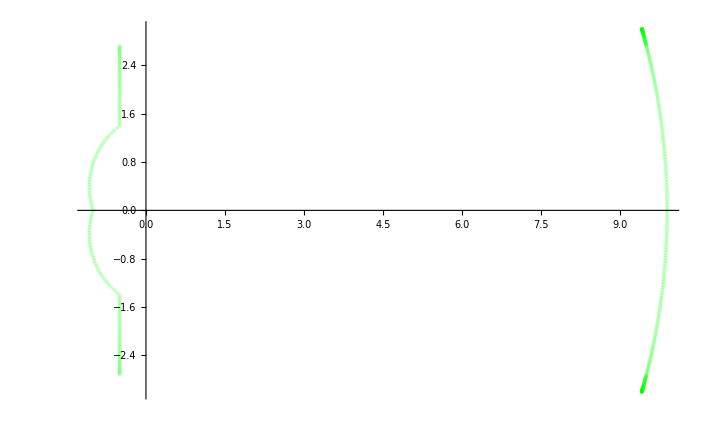

-Graphics-

-Graphics-

```mathematica
ListPlot[   {XY,XY1,XYgen,XYE},PlotStyle->{Blue,Purple,Directive[Opacity[0.2,Green]],Directive[PlotMarkers->Large, Orange]}  ]
ListPlot[ XYmN,PlotStyle->Pink]
ListPlot[ XYm,PlotStyle->Directive[Purple,Thick]]
```

```mathematica
CMS[ 0.50001 + ⅈ 5. ]
```

-0.653264+1.53655 ⅈ

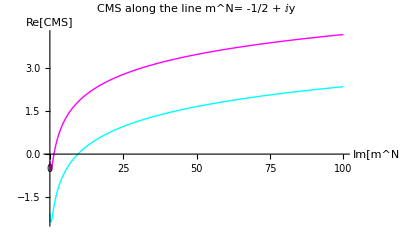

```mathematica
Plot[ {Re[CMS[ -0.50001 + ⅈ y ]], Re[CMS[-0.49999 + ⅈ y]]}, {y, 0., 100.}, 
	PlotStyle->{Directive[Magenta,Thick], Directive[Cyan,Thick]}, 
	   AxesLabel->{"Im[m^N]", "Re[CMS]"} ,PlotLabel->"CMS along the line m^N= -1/2 + ⅈy"]
```

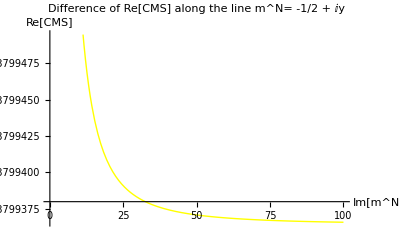

```mathematica
Plot[ {Re[CMS[ -0.50001 + ⅈ y ]]- Re[CMS[-0.49999 + ⅈ y]]}, {y, 0., 100.}, 
	PlotStyle->{Directive[Yellow,Thick]}, 
	   AxesLabel->{"Im[m^N]", "Re[CMS]"} ,PlotLabel->"Difference of Re[CMS] along the line m^N= -1/2 + ⅈy"]
```

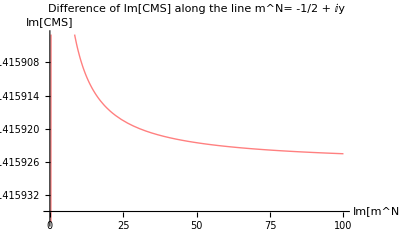

```mathematica
Plot[ {Im[CMS[ -0.50001 + ⅈ y ]]- Im[CMS[-0.49999 + ⅈ y]]}, {y, 0., 100.}, 
	PlotStyle->{Directive[Pink,Thick]}, 
	   AxesLabel->{"Im[m^N]", "Im[CMS]"} ,PlotLabel->"Difference of Im[CMS] along the line m^N= -1/2 + ⅈy"]
```

```mathematica
π/√3  // N
```

1.8138

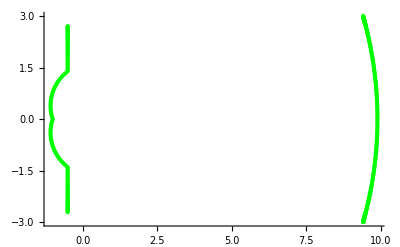

```mathematica
ListPlot[ XYgen, PlotStyle->Directive[Thick,Green] ]
```

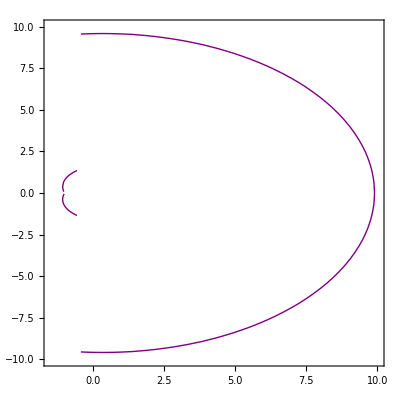

```mathematica
ContourPlot[   Re[CMS[x + ⅈ y]] == 0, { x , -1.5, 10}, {y, -10, 10}, ContourStyle->{ Thick, Purple }   ]
```

```mathematica
Plot3D[ Re[CMS[x + ⅈ y]], { x, -0.6, -0.4}, {y, 0., 10.}, AxesLabel->{"Re[m^N]","Im[m^N]", "Re[CMS]"}]
```

-Graphics3D-

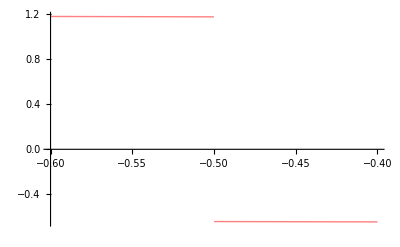

```mathematica
Plot[ Re[CMS[x + ⅈ 5.]], {x, -0.6, -0.4}, PlotStyle->Directive[Thick, Pink] ]
```

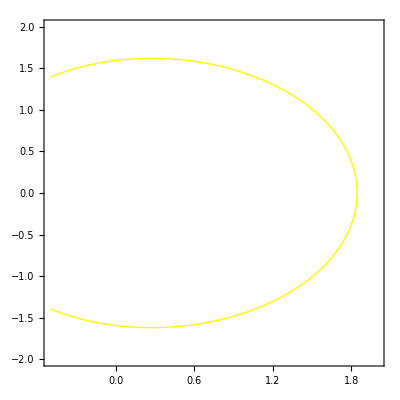

```mathematica
ContourPlot[   Re[CMSleft[x + ⅈ y]] == 0, { x , -0.5, +2}, {y, -2,2}, ContourStyle->{ Thick, Yellow }   ]
```

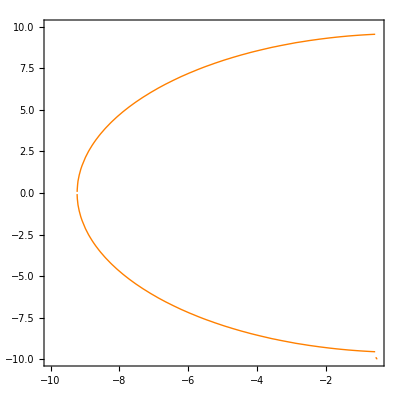

```mathematica
ContourPlot[   Re[CMSright[x + ⅈ y]] == 0, { x , -10, -0.5}, {y, -10, 10}, ContourStyle->{ Thick, Orange }   ]
```

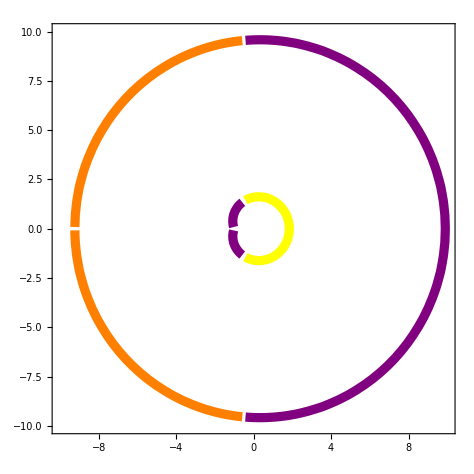

```mathematica
ContourPlot[   { Re[CMS[x + ⅈ y]] == 0,
		          Re[CMSleft[x + ⅈ y]] == 0,
		          Re[CMSright[x + ⅈ y]] == 0 }, 
                             { x , -10, 10}, { y, -10, 10 },
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ], 
                                                             Directive[ Thickness[0.014], Yellow ], 
                                                             Directive[ Thickness[0.014], Orange ] }   ]
```

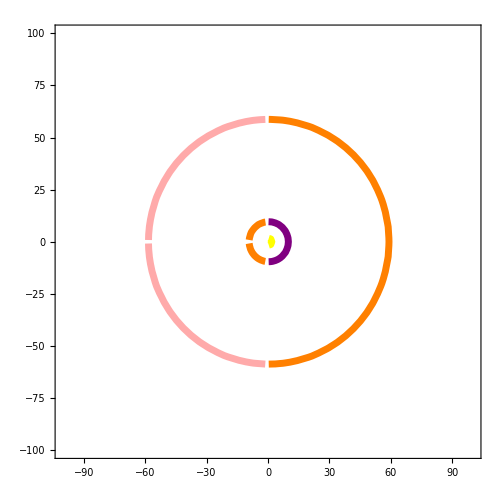

```mathematica
ContourPlot[   {  Re[CMS[x + ⅈ y]] == 0,
		          Re[CMSleft[x + ⅈ y]] == 0,
		          Re[CMSright[x + ⅈ y]] == 0,
			   Re[CMSright[x + ⅈ y] - (2 π ⅈ m0[x + ⅈ y])/(m1[x + ⅈ y] - m0[x + ⅈ y])] == 0 },
                             { x , -100, 100}, { y, -100, 100 },
                             ContourStyle->{ Directive[ Thickness[0.01], Purple ], 
                                                             Directive[ Thickness[0.01], Yellow ], 
                                                             Directive[ Thickness[0.01], Orange ],
						    Directive[ Thickness[0.01], Lighter[Pink] ]  }   ]
```

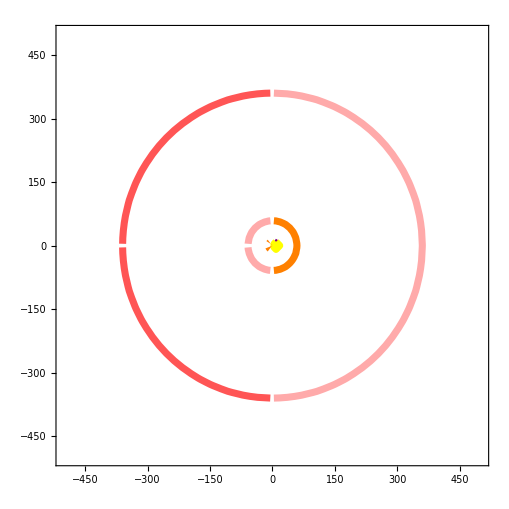

```mathematica
ContourPlot[   {  Re[CMS[x + ⅈ y]] == 0,
		          Re[CMSleft[x + ⅈ y]] == 0,
		          Re[CMSright[x + ⅈ y]] == 0,
			 Re[CMSright[x + ⅈ y] - (2 π ⅈ m0[x + ⅈ y])/(m1[x + ⅈ y] - m0[x + ⅈ y])] == 0 ,
			 Re[CMSright[x + ⅈ y] - 2(2 π ⅈ m0[x + ⅈ y])/(m1[x + ⅈ y] - m0[x + ⅈ y])] == 0},
                             { x , -500, 500}, { y, -500, 500 },
                             ContourStyle->{ Directive[ Thickness[0.01], Purple ], 
                                                             Directive[ Thickness[0.01], Yellow ], 
                                                             Directive[ Thickness[0.01], Orange ],
						    Directive[ Thickness[0.01], Lighter[Pink] ],
						    Directive[ Thickness[0.01], Lighter[Red]]  }   ]
```

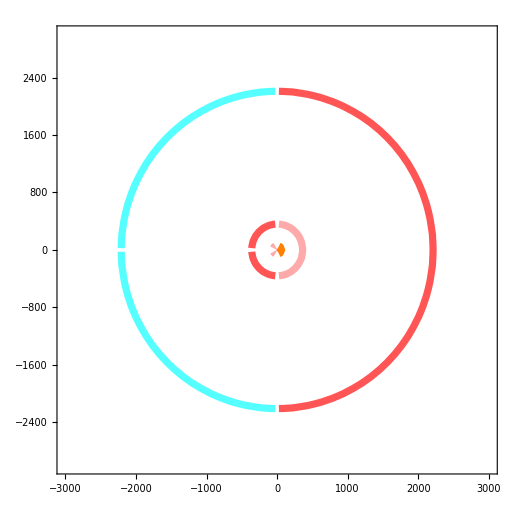

```mathematica
ContourPlot[   {  Re[CMS[x + ⅈ y]] == 0,
		           Re[CMSleft[x + ⅈ y]] == 0,
		           Re[CMSright[x + ⅈ y]] == 0,
		           Re[CMSright[x + ⅈ y] - (2 π ⅈ m0[x + ⅈ y])/(m1[x + ⅈ y] - m0[x + ⅈ y])] == 0 ,
		           Re[CMSright[x + ⅈ y] - 2(2 π ⅈ m0[x + ⅈ y])/(m1[x + ⅈ y] - m0[x + ⅈ y])] == 0,
                              Re[CMSright[x + ⅈ y] - 3(2 π ⅈ m0[x + ⅈ y])/(m1[x + ⅈ y] - m0[x + ⅈ y])] == 0  },
                             { x , -3000, 3000}, { y, -3000, 3000 },
                             ContourStyle->{ Directive[ Thickness[0.01], Purple ], 
                                                             Directive[ Thickness[0.01], Yellow ], 
                                                             Directive[ Thickness[0.01], Orange ],
						    Directive[ Thickness[0.01], Lighter[Pink] ],
						    Directive[ Thickness[0.01], Lighter[Red]],
                                                             Directive[ Thickness[0.01], Lighter[Cyan]]   }   ]
```

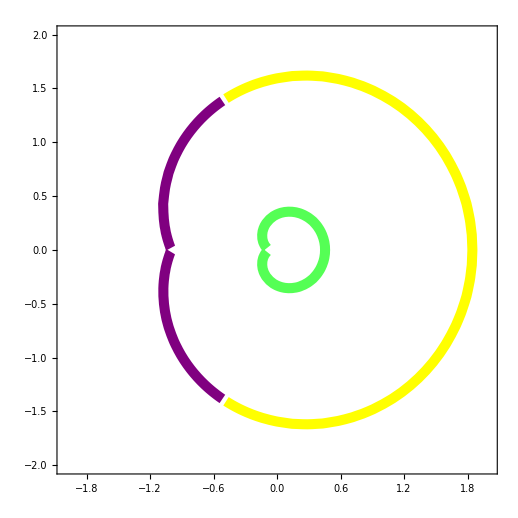

```mathematica
ContourPlot[   { Re[ CMS[x + ⅈ y] ] == 0,
		          Re[ CMSleft[x + ⅈ y] ] == 0,
			Re[ CMSFrac[x + ⅈ y,-2/3,-2/3] ] == 0 }, 
                             { x , -2, 2 }, { y, -2,2 },
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ], 
                                                             Directive[ Thickness[0.014], Yellow ],
						    Directive[ Thickness[0.014], Lighter[Green] ] }   ]
```

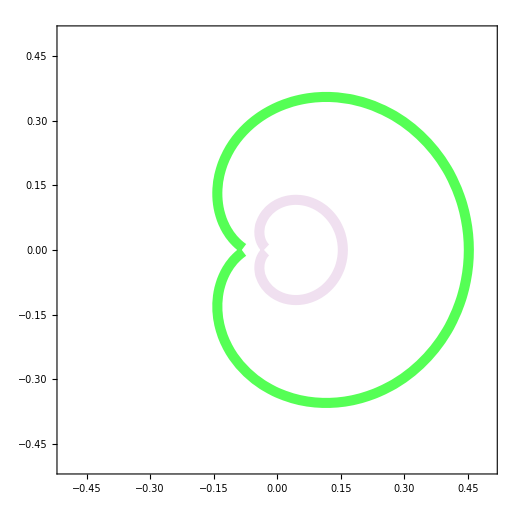

```mathematica
ContourPlot[   { Re[ CMS[x + ⅈ y] ] == 0,
		          Re[ CMSleft[x + ⅈ y] ] == 0,
			Re[ CMSFrac[x + ⅈ y,-2/3,-2/3] ] == 0,
			Re[ CMSFrac[x + ⅈ y,-3/3,-3/3] ] == 0  }, 
                             { x , -0.5, 0.5 }, { y, -0.5,0.5 },
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ], 
                                                             Directive[ Thickness[0.014], Yellow ],
						    Directive[ Thickness[0.014], Lighter[Green] ],
						    Directive[ Thickness[0.014], LightPurple] }   ]
```

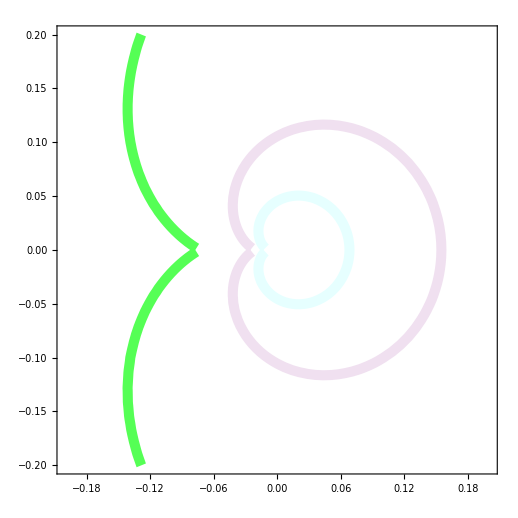

```mathematica
ContourPlot[   { Re[ CMS[x + ⅈ y] ] == 0,
		          Re[ CMSleft[x + ⅈ y] ] == 0,
			Re[ CMSFrac[x + ⅈ y,-2/3,-2/3] ] == 0,
			Re[ CMSFrac[x + ⅈ y,-3/3,-3/3] ] == 0 ,
			Re[ CMSFrac[x + ⅈ y,-4/3,-4/3] ] == 0 }, 
                             { x , -0.2, 0.2 }, { y, -0.2,0.2 },
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ], 
                                                             Directive[ Thickness[0.014], Yellow ],
						    Directive[ Thickness[0.014], Lighter[Green] ],
						    Directive[ Thickness[0.014], LightPurple],
						    Directive[ Thickness[0.014], LightCyan] }   ]
```